```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
tpdf=PDF[TransformedDistribution[u v,{u\[Distributed]BetaDistribution[1,1],v\[Distributed]BetaDistribution[3/2,1/2]}],x]
```

```mathematica
fTwoDist[η_]:=PDF[BetaDistribution[η,1/2],x]
```

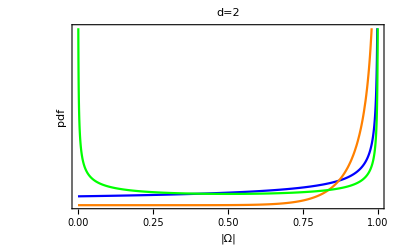

```mathematica
g1=Plot[{fTwoDist[1],fTwoDist[10],fTwoDist[0.5]},{x,0,1},PlotRange->{Full,{0,10}},PlotStyle->{Blue,Orange,Green},Frame->{True,True,False,False},FrameTicks->{True,False},BaseStyle->{FontSize->16},FrameLabel->{"|Ω|","pdf"},PlotLabel->"d=2"]
```

```mathematica
fThreePDF[η_]:=PDF[TransformedDistribution[u v,{u\[Distributed]BetaDistribution[η,1],v\[Distributed]BetaDistribution[η+(1/2),1/2]}],x]
uPDF = fPDF[1]
hPDF = fPDF[10]
lPDF = fPDF[0.5]
```

```mathematica
uPDF=Piecewise[{{Indeterminate, x==0}, {(-(2 √x)/(√(1-x))+(2 x)/(√(-(-1+x) x))+4 ArcCos[√x])/π, 0<x<1}, {0, True}}];
```

```mathematica
hPDF=Piecewise[{{-1/(14549535 π)2 ((41287680 x^(19/2))/(√(1-x))-14549535/(2 √(-(-1+x) x))+(14549535 (1-2 x))/(2 √(-(-1+x) x))-(4849845 x^2 (-3+4 x))/(√(-(-1+x) x^3))-(3879876 x^4 (-5+6 x))/(√(-(-1+x) x^5))-(3325608 x^6 (-7+8 x))/(√(-(-1+x) x^7))-(2956096 x^8 (-9+10 x))/(√(-(-1+x) x^9))-(2687360 x^10 (-11+12 x))/(√(-(-1+x) x^11))-(2480640 x^12 (-13+14 x))/(√(-(-1+x) x^13))-(2315264 x^14 (-15+16 x))/(√(-(-1+x) x^15))-(2179072 x^16 (-17+18 x))/(√(-(-1+x) x^17))-(2064384 x^18 (-19+20 x))/(√(-(-1+x) x^19))-825753600 x^9 ArcCos[√x]), 0<x<1}, {0, True}}];
```

```mathematica
lPDF=Piecewise[{{Indeterminate, x==0}, {1/2 (-1/(√(1-x))+1./(√(1.-1. x))+ArcCos[√x]/(√x)), 0<x<1}, {0, True}}];
```

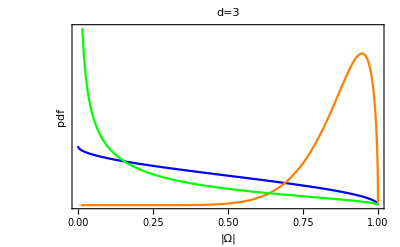

```mathematica
g2=Plot[{uPDF,hPDF,lPDF},{x,0,1},PlotRange->{Full,{0,6}},PlotStyle->{Blue,Orange,Green},Frame->{True,True,False,False},FrameTicks->{True,False},BaseStyle->{FontSize->16},FrameLabel->{"|Ω|","pdf"},PlotLabel->"d=3"]
```

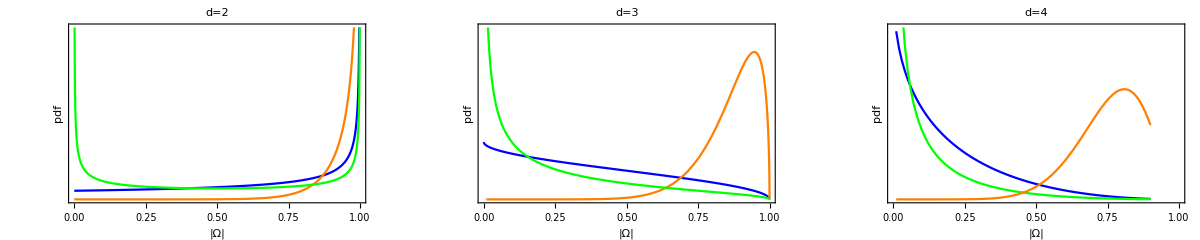

```mathematica
gFinal=Show[GraphicsRow[{g1,g2,g3}],ImageSize->1200]
```

```mathematica
Export["Distributions_LKJ_determinants.pdf",gFinal]
```

Distributions_LKJ_determinants.pdf

## Now implementing from http://mathematica.stackexchange.com/questions/91407/distribution-over-the-product-of-three-or-n-independent-beta-random-variables

```mathematica
aPDFFour=(27/60) Pi MeijerG[{{},{3/2,3/2,3/2}},{{0,1/2,1},{}},x];
```

```mathematica
aList = ParallelTable[{x,aPDFFour},{x,0.01,0.9,0.01}];
aList = Join[aList,Table[{x,0},{x,0.91,1,0.01}]];
```

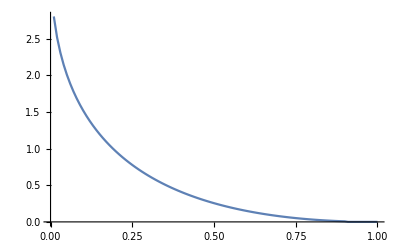

```mathematica
ListLinePlot[aList]
```

## A few different methods for working this out

```mathematica
f1 = Simplify[PDF[BetaDistribution[1,3/2],x],0<x<1]; domain[f1] = {x,0,1};
f2 = Simplify[PDF[BetaDistribution[3/2,1],x],0<x<1];domain[f2] = {x,0,1};
f3 = Simplify[PDF[BetaDistribution[2,1/2],x],0<x<1];domain[f3] = {x,0,1};
```

```mathematica
g=TransformProduct[{f2,f3},y];
domain[g]={y,0,1};
h = TransformProduct[{g,f1},z]
```

Piecewise[{{27/32 π MeijerG[{{},{3/2,3/2,3/2}},{{0,1/2,1},{}},z], 0<z<1}, {0, True}}]

## From Mathematica stack exchange (the link above). This should give the distribution for n Beta distributions multiplied together

```mathematica
ClearAll[pdfProductBeta];
pdfProductBeta[α_/;VectorQ[α,NumericQ],β_/;VectorQ[β,NumericQ],x_Symbol]/;Dimensions[α]==Dimensions[β]:=Module[{k},k=Times@@(Gamma[Plus@@#]/Gamma[#[[1]]]&/@(Transpose@{α,β}));
k MeijerG[{{},α+β-1},{α-1,{}},x]]
```

```mathematica
fEtaThreeProduct[η_,x_]:=Module[{a={η,η+(1/2),η+1},b={3/2,1,1/2}}, pdfProductBeta[a,b,y]/.{y->x}]
```

```mathematica
productNBeta[numBeta_Integer,η_,x_]:=Module[{a=Table[η+((j-1)/2),{j,1,numBeta,1}],b=Table[((numBeta+1)-j)/2,{j,1,numBeta,1}]},pdfProductBeta[a,b,y]/.{y->x}]
determinantDist[d_Integer,η_,x_]:=productNBeta[d-1,η,x]
```

```mathematica
lEtaThree1=ParallelTable[{x,determinantDist[4,1,x]},{x,0.01,0.9,0.01}];
```

```mathematica
lEtaThreeHalf=ParallelTable[{x,determinantDist[4,0.5,x]},{x,0.01,0.9,0.01}];
```

```mathematica
lEtaThreeTen=ParallelTable[{x,determinantDist[4,10,x]},{x,0.01,0.9,0.01}];
```

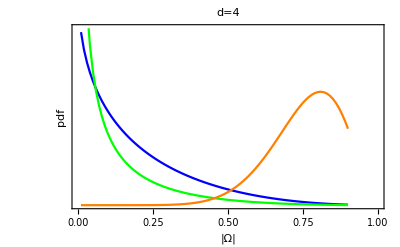

```mathematica
g3=ListLinePlot[{lEtaThree1,lEtaThreeHalf,lEtaThreeTen},PlotRange->{{0,1},Automatic},PlotStyle->{Blue,Green,Orange},Frame->{True,True,False,False},FrameTicks->{True,False},BaseStyle->{FontSize->16},FrameLabel->{"|Ω|","pdf"},PlotLabel->"d=4"]
```

```mathematica
f1 = Simplify[PDF[NormalDistribution[],x],0<x<1]; domain[f1] = {x,0,1};
f2 = Simplify[PDF[NormalDistribution[],x],0<x<1]; domain[f2] = {x,0,1};
```